```mathematica
(*导入结果*)
```

```mathematica
a=Import["G:\\calc-online\\gpd\\k-result\\diagram-l-q-n.wdx"];
```

```mathematica
(*带入必须的数值，最后结果要乘个系数,图a直接结果是复数，图m，图k也是复数，图l是实数*)
(*向前极限的计算注意是xi逼近0，不是直接取0*)
```

```mathematica
{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1}
```

{MB→0.939,mm→0.1381,MM→0.939,ξ→0.1,Q^2→1,q3→0.977103,Λ→1}

```mathematica
{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1}
{MB->0.939,mm->0.1381,MM->0.939,ξ->0.3,Q^2->1,q3->0.76979246,Λ->1}
{MB->0.939,mm->0.1381,MM->0.939,ξ->0.4,Q^2->1,q3->0.52507004,Λ->1}
{MB->0.939,mm->0.1381,MM->0.939,ξ->0,Q^2->1,q3->1,Λ->1}
```

{MB→0.939,mm→0.1381,MM→0.939,ξ→0.2,Q^2→1,q3→0.904945,Λ→1}

{MB→0.939,mm→0.1381,MM→0.939,ξ→0.3,Q^2→1,q3→0.769792,Λ→1}

{MB→0.939,mm→0.1381,MM→0.939,ξ→0.4,Q^2→1,q3→0.52507,Λ→1}

```mathematica
(*q3=(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)
(-(0.6)^2(0.939)^2+(1-(0.3)^2))^(1/2)*)
```

```mathematica
(*注意这里对y的取值范围和k+之间有一个变换，不要搞混了，y的上下限取[-xi,xi]是第一段[0,-q+]，y取[xi,1]对应的就是第二段[-q+,(1+xi)P]*)
f1=Query[1,1]@a;
g1=Query[1,2]@a;
f2=Query[2,1]@a;
g2=Query[2,2]@a;
```

```mathematica
q[x_]=(-(2x)^2(0.939)^2+(1-x^2))^(1/2);
```

```mathematica
nf1=f1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Q^2->1,q3->q[0.001],Λ->1};
ng1=g1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Q^2->1,q3->q[0.001],Λ->1};
nf2=f2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Q^2->1,q3->q[0.001],Λ->1};
ng2=g2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Q^2->1,q3->q[0.001],Λ->1};
```

```mathematica
ref1[x_]=Simplify[nf1/.{y->x}];
ref2[x_]=Simplify[nf2/.{y->x}];
reg1[x_]=Simplify[ng1/.{y->x}];
reg2[x_]=Simplify[ng2/.{y->x}];
```

```mathematica
inf1[x_]=Hold[NIntegrate[ref1[x],{k3,0,∞},{θ,0,2π},WorkingPrecision->10]];
inf2[x_]=Hold[NIntegrate[ref2[x],{k3,0,∞},{θ,0,2π},WorkingPrecision->10]];
ing1[x_]=Hold[NIntegrate[reg1[x],{k3,0,∞},{θ,0,2π},WorkingPrecision->10]];
ing2[x_]=Hold[NIntegrate[reg2[x],{k3,0,∞},{θ,0,2π},WorkingPrecision->10]];
```

```mathematica
lf1=Table[{x,ReleaseHold[inf1[x]]},{x,-0.001,0.001,0.000001}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
lf2=Table[{x,ReleaseHold[inf2[x]]},{x,0.001,1,0.001}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
lf3=Table[{x,ReleaseHold[inf2[x]]},{x,0.001,0.001,0.00001}];
```

```mathematica
lg1=Table[{x,ReleaseHold[ing1[x]]},{x,-0.001,0.001,0.000001}];
```

```mathematica
lg2=Table[{x,ReleaseHold[ing2[x]]},{x,0.001,1,0.001}];
```

```mathematica
lg3=Table[{x,ReleaseHold[ing2[x]]},{x,0.001,0.001,0.00001}];
```

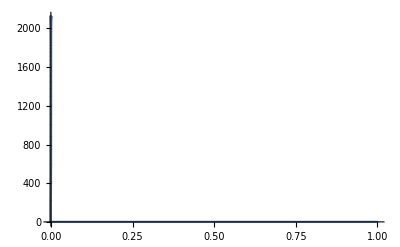

```mathematica
ListPlot[Join[lf1,lf2]]
```

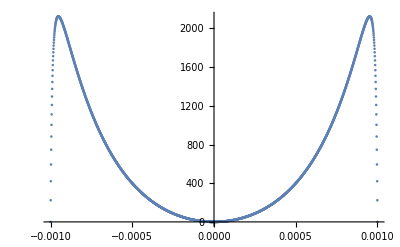

```mathematica
ListPlot[lf1]
```

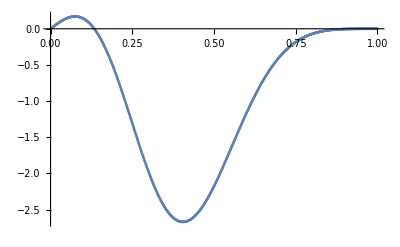

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ListPlot[lf2]
```